```mathematica
delta=1;w=-1-delta;b=1;
points=ListPointPlot3D[{{b/(2*delta+3),b/(2*delta+3),b/(2*delta+3)},
{b/(delta+2),b/(delta+2),0},
{b/(delta+2),0,b/(delta+2)},
{0,b/(delta+2),b/(delta+2)},
{b,0,0},{0,b,0},{0,0,b}}, PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
pos[x_]:=If[x>0,x,0];
f1[x_,y_,z_,i_]=(-1)^i(-x+pos[w*y+w*z+b]);
f2[x_,y_,z_,i_]=(-1)^i(-y+pos[w*x+w*z+b]);
f3[x_,y_,z_,i_]=(-1)^i(-z+pos[w*x+w*y+b]);
f={f1,f2,f3};
```

```mathematica
eps=1/10;ranges={{1/3-eps,1+eps},{-eps,1/3+eps},{-eps,eps}};
allranges={{-eps,1+eps},{-eps,1+eps},{-eps,1+eps}};
aranges={{b/(delta+2)-eps,b/(delta+2)+eps},{b/(delta+2)-eps,b/(delta+2)+eps},{-eps,b/(delta+2)+eps}};
```

```mathematica
Append[Table[If[k==i,ranges[[i]][[j]],x[k]],1+1]]
```

Append[{If[k==i,ranges⟦i⟧⟦j⟧,x[k]],If[k==i,ranges⟦i⟧⟦j⟧,x[k]]}]

```mathematica
As = Flatten[Table[Table[Reduce[Apply[f[[i]],Append[Table[If[k==i,ranges[[i]][[j]],x[k]],{k,3}],j+1]]<=0,Reals]&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]]),{j,2}],{i,3}]]
```

{x[2]≥1/60 (23-60 x[3])&&x[1]<7/30,x[2]≤1/20 (-1-20 x[3])&&x[1]>11/10,False,x[1]≤1/60 (17-60 x[3])&&x[2]>13/30,False,x[1]≤1/20 (9-20 x[2])&&x[3]>1/10}

```mathematica
all=Table[RegionPlot3D[As[[i]],{x[1],ranges[[1]][[1]]-0.0001,ranges[[1]][[2]]+0.0001},{x[2],ranges[[2]][[1]]-0.0001,ranges[[2]][[2]]+0.0001}, {x[3],ranges[[3]][[1]]-0.0001,ranges[[3]][[2]]+0.0001},AxesLabel->Automatic],{i,1}];Show[all]
```

-Graphics3D-

```mathematica
zeros=Flatten[Table[Table[Reduce[Apply[f[[i]],Append[Table[If[k==i,ranges[[i]][[j]],x[k]],{k,3}],j+1]]==0,Reals],{j,2}],{i,3}]]
```

{x[2]==1/60 (23-60 x[3]),x[2]==1/60 (17-60 x[3]),x[1]==1/60 (23-60 x[3]),x[1]==1/60 (17-60 x[3]),False,x[1]==1/60 (17-60 x[2])}

```mathematica
zeros[[1]][[2]]
```

1/60 (23-60 x[3])

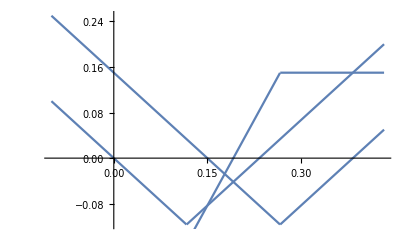

```mathematica
Show[Plot[f[[2]][ranges[[1]][[1]],zeros[[1]][[2]],x[3],0],{x[3],ranges[[3]][[1]],ranges[[3]][[2]]}],
Plot[f[[3]][ranges[[1]][[1]],zeros[[1]][[2]],x[3],0],{x[3],ranges[[3]][[1]],ranges[[3]][[2]]}],
Plot[-f[[2]][ranges[[1]][[1]],zeros[[1]][[2]],x[3],0]+f[[3]][ranges[[1]][[1]],zeros[[1]][[2]],x[3],0],{x[3],ranges[[3]][[1]],ranges[[3]][[2]]}]]
```

```mathematica
ranges
```

{{9997/30000,10003/30000},{9997/30000,10003/30000},{-1/10000,10003/30000}}

```mathematica
ImplicitRegion[As[[1]],{x[1],x[2]}]
```

ImplicitRegion[x[2]>1/60 (23-60 x[3])&&x[1]<7/30,{x[1],x[2]}]

```mathematica
3^5
```

243

```mathematica
Bs1 = Flatten[Table[Table[Table[Reduce[Apply[f[[Mod[i+1,3]]],Append[Table[If[(k==i)||(k==Mod[i+1,3]),ranges[[k]][[If[k==i,j,n]]],x[k]],{k,3}],n+1]]<0,Reals]
&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]])
&&(If[Mod[n+1,2]==0,x[Mod[i+1,3]]<ranges[[Mod[i+1,3]]][[n]], x[Mod[i+1,3]]>ranges[[Mod[i+1,3]]][[n]]]),{j,2}],{i,3}],{n,2}]];
add=2;Bs2 = Flatten[Table[Table[Table[Reduce[Apply[f[[Mod[i+add,3]]],Append[Table[If[(k==i)||(k==Mod[i+add,3]),ranges[[k]][[If[k==i,j,n]]],x[k]],{k,3}],n+1]]<0,Reals]
&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]])
&&(If[Mod[n+1,2]==0,x[Mod[i+add,3]]<ranges[[Mod[i+add,3]]][[n]], x[Mod[i+add,3]]>ranges[[Mod[i+add,3]]][[n]]]),{j,2}],{i,3}],{n,2}]];
```

```mathematica
Length[Bs2]
```

12

```mathematica
kicsi=0.001;Bss=List[Bs1,Bs2];all=Table[Table[RegionPlot3D[Bss[[n]][[i]],{x[1],ranges[[1]][[1]]-kicsi,ranges[[1]][[2]]+kicsi},{x[2],ranges[[2]][[1]]-kicsi,ranges[[2]][[2]]+kicsi}, {x[3],ranges[[3]][[1]]-kicsi,ranges[[3]][[2]]+kicsi},AxesLabel->Automatic],{i,6}],{n,2}];Show[all,Axes->False]
```

-Graphics3D-

```mathematica
Cs = Flatten[Table[Table[Table[Table[Reduce[Apply[f[[n]],{ranges[[1]][[i]],ranges[[2]][[j]],ranges[[3]][[k]],n+1}]<0,Reals]
&&(If[Mod[i+1,2]==0,x[1]<ranges[[1]][[i]], x[1]>ranges[[1]][[i]]])
&&(If[Mod[j+1,2]==0,x[2]<ranges[[2]][[j]], x[2]>ranges[[2]][[j]]])
&&(If[Mod[k+1,2]==0,x[3]<ranges[[3]][[k]], x[3]>ranges[[3]][[k]]]),{i,2}],{j,2}],{k,2}],{n,3}]]
```

{False,False,False,x[1]>13/30&&x[2]>13/30&&x[3]<-1/10,x[1]<7/30&&x[2]<7/30&&x[3]>13/30,x[1]>13/30&&x[2]<7/30&&x[3]>13/30,x[1]<7/30&&x[2]>13/30&&x[3]>13/30,x[1]>13/30&&x[2]>13/30&&x[3]>13/30,x[1]<7/30&&x[2]<7/30&&x[3]<-1/10,x[1]>13/30&&x[2]<7/30&&x[3]<-1/10,x[1]<7/30&&x[2]>13/30&&x[3]<-1/10,False,False,False,False,False,False,False,False,False,x[1]<7/30&&x[2]<7/30&&x[3]>13/30,x[1]>13/30&&x[2]<7/30&&x[3]>13/30,x[1]<7/30&&x[2]>13/30&&x[3]>13/30,x[1]>13/30&&x[2]>13/30&&x[3]>13/30}

```mathematica
Length[Cs]
```

24

```mathematica
kicsi=0.01;all=Table[RegionPlot3D[Cs[[Length[Cs]]],{x[1],ranges[[1]][[1]]-kicsi,ranges[[1]][[2]]+kicsi},{x[2],ranges[[2]][[1]]-kicsi,ranges[[2]][[2]]+kicsi}, {x[3],ranges[[3]][[1]]-kicsi,ranges[[3]][[2]]+kicsi},AxesLabel->Automatic],{i,6}];
Show[all,Axes->False]
```

-Graphics3D-

```mathematica
Cs= Flatten[Table[Table[Table[Table[Reduce[Apply[f[[n]],{ranges[[1]][[i]],ranges[[2]][[j]],ranges[[3]][[k]],If[n==1,i,If[n==2,j,k]]}]<0,Reals],{i,2}],{j,2}],{k,2}],{n,3}]]
```

```mathematica
pos[x_]:=If[x>0,x,0];
f1[x_,y_,z_,i_]=(-1)^i(-x+pos[w*y+w*z+b]);
f2[x_,y_,z_,i_]=(-1)^i(-y+pos[w*x+w*z+b]);
f3[x_,y_,z_,i_]=(-1)^i(-z+pos[w*x+w*y+b]);
f={f1,f2,f3};
```

```mathematica
delta=1;w=-1-delta;b=1;
eps=1/10;
ranges={{b/(delta+2)-eps,b/(delta+2)+eps},{b/(delta+2)-eps,b/(delta+2)+eps},{-eps,b/(delta+2)+eps}};
points=ListPointPlot3D[{{b/(2*delta+3),b/(2*delta+3),b/(2*delta+3)},
{b/(delta+2),b/(delta+2),0},
{b/(delta+2),0,b/(delta+2)},
{0,b/(delta+2),b/(delta+2)},
{b,0,0},{0,b,0},{0,0,b}}, PlotRange->{{0,1},{0,1},{0,1}},BoxRatios->{1,1,1},PlotStyle->Orange];
```

```mathematica
As = Flatten[Table[Table[Reduce[Apply[f[[i]],Append[Table[If[k==i,ranges[[i]][[j]],x[k]],{k,3}],j+1]]<=0,Reals]&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]]),{j,2}],{i,3}]];a=Table[RegionPlot3D[As[[i]],{x[1],ranges[[1]][[1]]-0.0001,ranges[[1]][[2]]+0.0001},{x[2],ranges[[2]][[1]]-0.0001,ranges[[2]][[2]]+0.0001}, {x[3],ranges[[3]][[1]]-0.0001,ranges[[3]][[2]]+0.0001},AxesLabel->Automatic,Mesh->None],{i,1}];Bs1 = Flatten[Table[Table[Table[Reduce[Apply[f[[Mod[i+1,3]]],Append[Table[If[(k==i)||(k==Mod[i+1,3]),ranges[[k]][[If[k==i,j,n]]],x[k]],{k,3}],n+1]]<0,Reals]
&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]])
&&(If[Mod[n+1,2]==0,x[Mod[i+1,3]]<ranges[[Mod[i+1,3]]][[n]], x[Mod[i+1,3]]>ranges[[Mod[i+1,3]]][[n]]]),{j,2}],{i,3}],{n,2}]];
add=2;Bs2 = Flatten[Table[Table[Table[Reduce[Apply[f[[Mod[i+add,3]]],Append[Table[If[(k==i)||(k==Mod[i+add,3]),ranges[[k]][[If[k==i,j,n]]],x[k]],{k,3}],n+1]]<0,Reals]
&&(If[Mod[j+1,2]==0,x[i]<ranges[[i]][[j]], x[i]>ranges[[i]][[j]]])
&&(If[Mod[n+1,2]==0,x[Mod[i+add,3]]<ranges[[Mod[i+add,3]]][[n]], x[Mod[i+add,3]]>ranges[[Mod[i+add,3]]][[n]]]),{j,2}],{i,3}],{n,2}]];kicsi=0.001;Bss=List[Bs1,Bs2];b=Table[Table[RegionPlot3D[Bss[[n]][[i]],{x[1],ranges[[1]][[1]]-kicsi,ranges[[1]][[2]]+kicsi},{x[2],ranges[[2]][[1]]-kicsi,ranges[[2]][[2]]+kicsi}, {x[3],ranges[[3]][[1]]-kicsi,ranges[[3]][[2]]+kicsi},AxesLabel->Automatic],{i,6}],{n,2}];
Cs= Flatten[Table[Table[Table[Table[If[Reduce[Apply[f[[n]],{ranges[[1]][[i]],ranges[[2]][[j]],ranges[[3]][[k]],If[n==1,i,If[n==2,j,k]+1]}]<0,Reals],{ranges[[1]][[i]],ranges[[2]][[j]],ranges[[3]][[k]]}],{i,2}],{j,2}],{k,2}],{n,3}],3];
c=ListPointPlot3D[Cs];
Show[a,b,c,points]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

General::stop: Further output of Reduce::nsmet will be suppressed during this calculation.

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

General::stop: Further output of Reduce::inex will be suppressed during this calculation.

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Join::heads: Heads Reduce and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

-Graphics3D-

```mathematica
Cs
```

{True,False,True,True,False,True,False,True,True,True,False,True,False,False,True,True,True,True,True,True,True,True,True,True}

```mathematica
ranges={{b/(delta+2)-eps,b+eps},{b/(delta+2)-eps,b/(delta+2)+eps},{-eps,eps}};
```

```mathematica
ranges
```

{{7/30,11/10},{7/30,13/30},{-1/10,1/10}}